```mathematica
SetDirectory["C:\\Users\\Caden Gobat\\Documents\\GitHub\\PHYS-3181\\homework2"]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework2

```mathematica
coarseDataMP=ReadList["P1_025_midpoint.log",{Number,Number}]
medDataMP=ReadList["P1_010_midpoint.log",{Number,Number}]
fineDataMP=ReadList["P1_002_midpoint.log",{Number,Number}]
```

{{0.,0.},{0.25,0.283287},{0.5,0.647035},{0.75,1.1141},{1.,1.71382}}

{{0.,0.},{0.1,0.105127},{0.2,0.221311},{0.3,0.349713},{0.4,0.49162},{0.5,0.648451},{0.6,0.821776},{0.7,1.01333},{0.8,1.22503},{0.9,1.459},{1.,1.71757}}

{{0.,0.},{0.02,0.020201},{0.04,0.04081},{0.06,0.061836},{0.08,0.083286},{0.1,0.105169},{0.12,0.127495},{0.14,0.150271},{0.16,0.173508},{0.18,0.197214},{0.2,0.221399},{0.22,0.246073},{0.24,0.271245},{0.26,0.296925},{0.28,0.323124},{0.3,0.349853},{0.32,0.377121},{0.34,0.404941},{0.36,0.433322},{0.38,0.462277},{0.4,0.491817},{0.42,0.521953},{0.44,0.552698},{0.46,0.584064},{0.48,0.616064},{0.5,0.64871},{0.52,0.682016},{0.54,0.715995},{0.56,0.75066},{0.58,0.786025},{0.6,0.822105},{0.62,0.858914},{0.64,0.896466},{0.66,0.934777},{0.68,0.973862},{0.7,1.01374},{0.72,1.05442},{0.74,1.09592},{0.76,1.13826},{0.78,1.18145},{0.8,1.22552},{0.82,1.27048},{0.84,1.31635},{0.86,1.36314},{0.88,1.41088},{0.9,1.45958},{0.92,1.50927},{0.94,1.55996},{0.96,1.61167},{0.98,1.66443}}

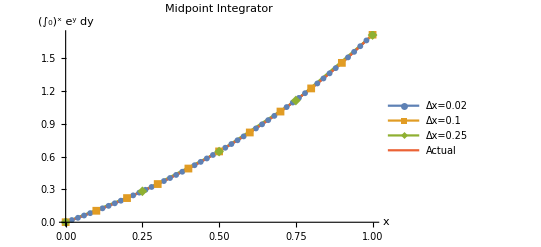

```mathematica
midfig = ListLinePlot[{fineDataMP,medDataMP,coarseDataMP,Table[{x,Exp[x]-1},{x,0,1,0.01}]},PlotLegends->{"Δx=0.02","Δx=0.1","Δx=0.25","Actual"},PlotMarkers->{{Automatic,6},{Automatic,8},{Automatic,10},{None,6}},PlotLabel->"Midpoint Integrator",AxesLabel->{"x","(∫_0)^x e^y dy"}]
```

```mathematica
coarseDataLH=ReadList["P1_025_left.log",{Number,Number}]
medDataLH=ReadList["P1_010_left.log",{Number,Number}]
fineDataLH=ReadList["P1_002_left.log",{Number,Number}]
```

{{0.,0.},{0.25,0.25},{0.5,0.571006},{0.75,0.983187},{1.,1.51244}}

{{0.,0.},{0.1,0.1},{0.2,0.210517},{0.3,0.332657},{0.4,0.467643},{0.5,0.616826},{0.6,0.781698},{0.7,0.96391},{0.8,1.16529},{0.9,1.38784},{1.,1.6338}}

{{0.,0.},{0.02,0.02},{0.04,0.040404},{0.06,0.06122},{0.08,0.082457},{0.1,0.104123},{0.12,0.126226},{0.14,0.148776},{0.16,0.171782},{0.18,0.195252},{0.2,0.219196},{0.22,0.243624},{0.24,0.268546},{0.26,0.293971},{0.28,0.319909},{0.3,0.346372},{0.32,0.373369},{0.34,0.400912},{0.36,0.429011},{0.38,0.457677},{0.4,0.486923},{0.42,0.516759},{0.44,0.547199},{0.46,0.578253},{0.48,0.609934},{0.5,0.642256},{0.52,0.67523},{0.54,0.708871},{0.56,0.743191},{0.58,0.778204},{0.6,0.813925},{0.62,0.850367},{0.64,0.887546},{0.66,0.925476},{0.68,0.964171},{0.7,1.00365},{0.72,1.04392},{0.74,1.08501},{0.76,1.12693},{0.78,1.1697},{0.8,1.21333},{0.82,1.25784},{0.84,1.30325},{0.86,1.34958},{0.88,1.39684},{0.9,1.44506},{0.92,1.49425},{0.94,1.54443},{0.96,1.59563},{0.98,1.64787},{1.,1.70116}}

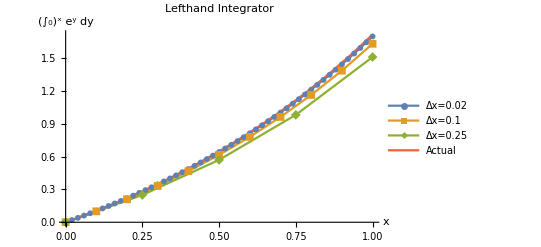

```mathematica
leftfig = ListLinePlot[{fineDataLH,medDataLH,coarseDataLH,Table[{x,Exp[x]-1},{x,0,1,0.01}]},PlotLegends->{"Δx=0.02","Δx=0.1","Δx=0.25","Actual"},PlotMarkers->{{Automatic,6},{Automatic,8},{Automatic,10},{None,6}},PlotLabel->"Lefthand Integrator",AxesLabel->{"x","(∫_0)^x e^y dy"}]
```

```mathematica
Export["P1_LH.png",leftfig]
Export["P1_MP.png",midfig]
```

P1_LH.png

P1_MP.png

```mathematica
binErr=ReadList["P2_err.log",{Number,Number}]
```

{{0.1,0.0491668},{0.01,0.00499167},{0.001,0.000499917},{0.0001,0.0000499992},{0.00001,4.99999×10^-6},{1.×10^-6,5.×10^-7},{1.×10^-7,5.×10^-8},{1.×10^-8,5.00024×10^-9},{1.×10^-9,5.00055×10^-10}}

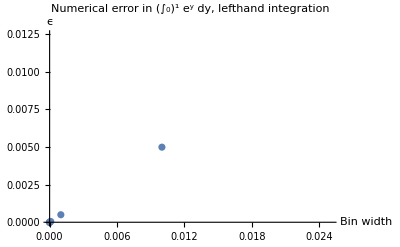

```mathematica
errorPlot=ListPlot[binErr,PlotLabel->"Numerical error in (∫_0)^1 e^y dy, lefthand integration",AxesLabel->{"Bin width","ϵ"}]
```

```mathematica
Export["P2.png",errorPlot]
```

P2.png

```mathematica
(Log[binErr[[5,2]]]-Log[binErr[[3,2]]])/(Log[binErr[[5,1]]]-Log[binErr[[3,1]]])
```

0.999964

```mathematica
mpErr=ReadList["P3_err.log",{Number,Number}]
```

{{0.1,0.000416545},{0.01,4.16665×10^-6},{0.001,4.16667×10^-8},{0.0001,4.16672×10^-10},{0.00001,4.1683×10^-12},{1.×10^-6,4.7×10^-14},{1.×10^-7,1.52×10^-14},{1.×10^-8,5.722×10^-13},{1.×10^-9,6.56×10^-14}}

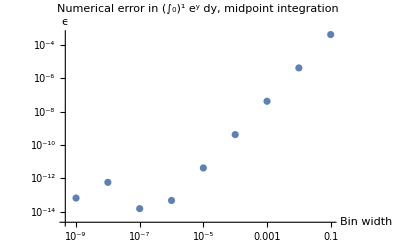

```mathematica
newerrorPlot=ListLogLogPlot[mpErr,PlotLabel->"Numerical error in (∫_0)^1 e^y dy, midpoint integration",AxesLabel->{"Bin width","ϵ"}]
```

```mathematica
Export["P3.png",newerrorPlot]
```

P3.png

```mathematica
(Log[mpErr[[5,2]]]-Log[mpErr[[3,2]]])/(Log[mpErr[[5,1]]]-Log[mpErr[[3,1]]])
```

1.99991

```mathematica
pendula=ReadList["pendulum.log",{Number,Number}]
```

{{5.,0.0000908375},{6.,0.000300377},{7.,0.000548119},{8.,0.000834115},{9.,0.00115843},{10.,0.00152112},{11.,0.00192227},{12.,0.00236196},{13.,0.00284029},{14.,0.00335736},{15.,0.00391328},{16.,0.00450816},{17.,0.00514213},{18.,0.00581533},{19.,0.0065279},{20.,0.00727999},{21.,0.00807177},{22.,0.0089034},{23.,0.00977506},{24.,0.010687},{25.,0.0116393},{26.,0.0126322},{27.,0.013666},{28.,0.0147408},{29.,0.015857},{30.,0.0170147},{31.,0.0182143},{32.,0.0194559},{33.,0.0207398},{34.,0.0220664},{35.,0.023436},{36.,0.0248488},{37.,0.0263052},{38.,0.0278055},{39.,0.02935},{40.,0.0309392},{41.,0.0325733},{42.,0.0342528},{43.,0.0359781},{44.,0.0377495},{45.,0.0395675},{46.,0.0414325},{47.,0.043345},{48.,0.0453054},{49.,0.0473142},{50.,0.0493719}}

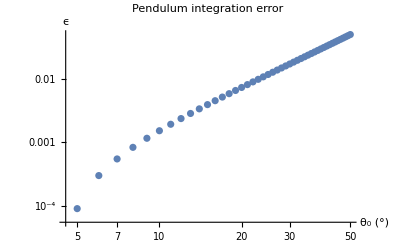

```mathematica
pendulumPlot=ListLogLogPlot[pendula,PlotLabel->"Pendulum integration error",AxesLabel->{"θ_0 (°)","ϵ"}]
```

```mathematica
Export["pendulum.png",pendulumPlot]
```

pendulum.png

```mathematica
(Log[0.0309391928066388]-Log[0.0493719439683806])/(Log[40]-Log[50])
```

2.09443